```mathematica
x[t_]:=UnitStep[t-1]*(1-UnitStep[t-2])
```

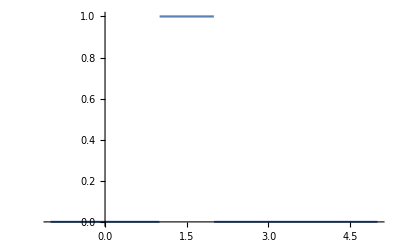

```mathematica
Plot[x[t],{t,-1,5}]
```

```mathematica
h[t_]:=UnitStep[t]*Piecewise[{{1/Exp[t-1],True}},1]
```

```mathematica
Dynamic@Plot[h[t],{t,-1,5}]
```

```mathematica
y=Convolve[h[t],x[t],t,u];
```

```mathematica
Dynamic@Plot[y,{u,-1,5}]
```

```mathematica
Inverse[Integrate[f[t],t]]
```

Inverse[∫f[t]ⅆt]

```mathematica
Echo[Simplify@InverseLaplaceTransform[1/(s(s+1)(s-5)),s,t]];
Plot[Re[%],{t,0,10}]
```

1/30 ⅇ^-t (5-6 ⅇ^t+ⅇ^(6 t))

-Graphics-

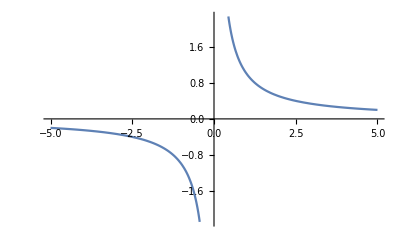

```mathematica
Plot[1/x,{x,-5,5}]
```

```mathematica
InverseLaplaceTransform[1/(s+4),s,t]
```

ⅇ^(-4 t)

```mathematica
LaplaceTransform[DiracDelta[t],t,s]
```

1

```mathematica
fs = k(2y[t]+x[t])
fd=-c y'[t]
```

k (x[t]+2 y[t])

-c y'[t]

```mathematica
diffeq=m y''[t]==fs+fd
```

m y''[t]==k (x[t]+2 y[t])-c y'[t]

```mathematica
DSolve[diffeq,{y[t]},{t}];
```

```mathematica
LaplaceTransform[diffeq,t,s]
```

m (s^2 LaplaceTransform[y[t],t,s]-s y[0]-y'[0])==k LaplaceTransform[x[t],t,s]+2 k LaplaceTransform[y[t],t,s]-c (s LaplaceTransform[y[t],t,s]-y[0])

## Inclass

## Pass 1

```mathematica
ms=LaplaceTransform[Sin[.1t]*UnitStep[t],t,s]
sol=Simplify[InverseLaplaceTransform[-k/(m s^2 + k+c s)*ms,s,t]]*UnitStep[t];
```

0.1/(0.01+s^2)

```mathematica
p={k->3,m->1,c->.1};
Dynamic[sol2=sol/.p;
lines={sol2,D[sol2,t],D[sol2,{t,2}]};
Plot[Evaluate@lines[[1]],{t,0,100},PlotRange->Full,PlotLegends->{"x","v","a"}]]
```

## Manipulate

```mathematica
Manipulate[ms=LaplaceTransform[Sin[ω t]*UnitStep[t],t,s];
sol=Simplify[InverseLaplaceTransform[-k/(m s^2 + k+c s)*ms,s,t]]*UnitStep[t];,{ω,0,5}]
```

```mathematica
p={k->3,m->1,c->.1};
Dynamic[sol2=sol/.p;
lines={sol2,D[sol2,t],D[sol2,{t,2}]};
Plot[Evaluate@lines[[1]],{t,0,100},PlotRange->Full,PlotLegends->{"x","v","a"}]]
```